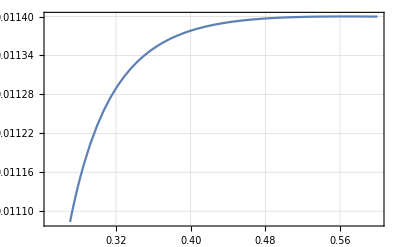

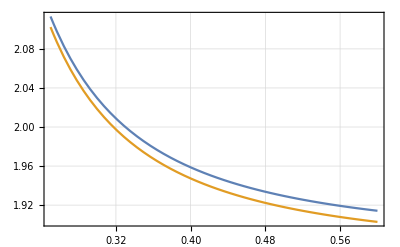

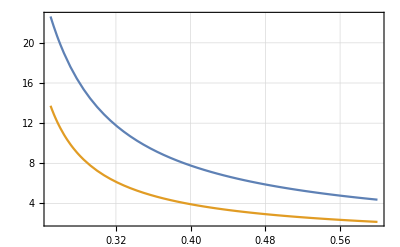

refrIndex$La3Ga5SiO14$Ordinary

(0.00005 * complexI) / numberE**(1.2011325347955075e15 * (-2.8e-7 + lambda)**2.0) + sqrt(1.0 + (2.4981088 * lambda**2.0) / (-1.6845031370328092e-14 + lambda**2.0))

refrIndex$La3Ga5SiO14$ExtraOrdinary

(0.0001 * complexI) / numberE**(1.2011325347955075e15 * (-2.8e-7 + lambda)**2.0) + sqrt(1.0 + (2.5408145 * lambda**2.0) / (-1.6679115500522497e-14 + lambda**2.0))

g11$La3Ga5SiO14

(lambda * ((6.278e-12 * lambda**2.0) / (-2.4335999999999998e-14 + lambda**2.0)**2.0 + 6.106e-12 / (-2.4335999999999998e-14 + lambda**2.0)) * (re((0.00005 * complexI) / numberE**(1.2011325347955075e15 * (-2.8e-7 + lambda)**2.0) + sqrt(1.0 + (2.4981088 * lambda**2.0) / (-1.6845031370328092e-14 + lambda**2.0))) + re((0.0001 * complexI) / numberE**(1.2011325347955075e15 * (-2.8e-7 + lambda)**2.0) + sqrt(1.0 + (2.5408145 * lambda**2.0) / (-1.6679115500522497e-14 + lambda**2.0))))) / 2

g33$La3Ga5SiO14

(3.0359999999999996e-12 * lambda * (re((0.00005 * complexI) / numberE**(1.2011325347955075e15 * (-2.8e-7 + lambda)**2.0) + sqrt(1.0 + (2.4981088 * lambda**2.0) / (-1.6845031370328092e-14 + lambda**2.0))) + re((0.0001 * complexI) / numberE**(1.2011325347955075e15 * (-2.8e-7 + lambda)**2.0) + sqrt(1.0 + (2.5408145 * lambda**2.0) / (-1.6679115500522497e-14 + lambda**2.0))))) / (-3.9204e-14 + lambda**2.0)

```mathematica
(*La3Ga5SiO14*)(*0.4 mkm<lambda<1.0 mkm*)mkm=10^-6;

(* , "2" -> "2.0", "3" -> "3.0", "4" -> "4.0" *)
replace[s_?StringQ]:= StringReplace[s, {"*" -> " * ", "/" -> " / ", "^" -> "**", "[" -> "(", "]" -> ")", "Sqrt" -> "sqrt", "Re" -> "re", "I" -> "complexI", "E" -> "numberE"}];

replace2[s_?StringQ]:= StringReplace[s, {" * **" -> "e", "(0. + " -> "(", "**2" -> "**2.0", "(1 + " -> "(1.0 + "}];

refrIndexSquared[lambda_,kCoeff_,lambdaNull_]:=1+kCoeff*lambda^2/(lambda^2-lambdaNull^2);
sigmaAbsorption[lambdaMidPoint_,lambdaHalfWidth_]:=(lambdaHalfWidth-lambdaMidPoint)/Log[2];
absorptionCoeff[lambda_,kAbsorption_,lambdaMidPoint_,lambdaHalfWidth_]:=kAbsorption*Exp[-(lambda-lambdaMidPoint)^2/sigmaAbsorption[lambdaMidPoint,lambdaHalfWidth]^2];

refrIndex[lambda_,kCoeff_,lambdaNull_,kAbsorption_,lambdaMidPoint_,lambdaHalfWidth_]:=Sqrt[refrIndexSquared[lambda,kCoeff,lambdaNull]]+I*absorptionCoeff[lambda,kAbsorption,lambdaMidPoint,lambdaHalfWidth];

gyration11Func[lambda_,refrIndAverageFunc_,a2Coeff_,a3Coeff_,lambda2Coeff_]:=lambda*refrIndAverageFunc[lambda]*((a2Coeff/(lambda^2-lambda2Coeff^2))+(a3Coeff*lambda^2/(lambda^2-lambda2Coeff^2)^2));

gyration33Func[lambda_,refrIndAverageFunc_,a1Coeff_,lambda1Coeff_]:=lambda*refrIndAverageFunc[lambda]*a1Coeff/(lambda^2-lambda1Coeff^2);

refrIndex$La3Ga5SiO14$Ordinary[lambda_]:=refrIndex[lambda,2.4981088,0.12978841 mkm,0.5*10^-4,0.28*mkm,0.3*mkm];

refrIndex$La3Ga5SiO14$ExtraOrdinary[lambda_]:=refrIndex[lambda,2.5408145,0.12914765 mkm,1.0*10^-4,0.28*mkm,0.3*mkm];

refrIndex$La3Ga5SiO14$Average[lambda_]:=(Re[refrIndex$La3Ga5SiO14$Ordinary[lambda]]+Re[refrIndex$La3Ga5SiO14$ExtraOrdinary[lambda]])/2;

g11$La3Ga5SiO14[lambda_]:=gyration11Func[lambda,refrIndex$La3Ga5SiO14$Average,0.6106*10^-11,0.6278*10^-11,0.156 mkm];

g33$La3Ga5SiO14[lambda_]:=gyration33Func[lambda,refrIndex$La3Ga5SiO14$Average,0.6072*10^-11,0.198 mkm];

Print[Plot[Re[refrIndex$La3Ga5SiO14$ExtraOrdinary[lmb mkm]]-Re[refrIndex$La3Ga5SiO14$Ordinary[lmb mkm]],{lmb,0.25,0.60}, Frame->True, GridLines->Automatic]];
Print[Plot[{Re[refrIndex$La3Ga5SiO14$ExtraOrdinary[lmb mkm]],Re[refrIndex$La3Ga5SiO14$Ordinary[lmb mkm]]},{lmb,0.25,0.60}, Frame->True, GridLines->Automatic]];
Print[Plot[{10^5*g11$La3Ga5SiO14[lmb mkm],10^5*g33$La3Ga5SiO14[lmb mkm]},{lmb,0.25,0.60}, Frame->True, GridLines->Automatic]];

Print["\n\nrefrIndex$La3Ga5SiO14$Ordinary"];
Print[refrIndex$La3Ga5SiO14$Ordinary[lambda]]
Print[replace2[replace[ToString[InputForm[refrIndex$La3Ga5SiO14$Ordinary[lambda]]]]]]

Print["\n\nrefrIndex$La3Ga5SiO14$ExtraOrdinary"];
Print[replace2[replace[ToString[InputForm[refrIndex$La3Ga5SiO14$ExtraOrdinary[lambda]]]]]]

Print["\n\ng11$La3Ga5SiO14"];
Print[replace2[replace[ToString[InputForm[g11$La3Ga5SiO14[lambda]]]]]]

Print["\n\ng33$La3Ga5SiO14"];
Print[replace2[replace[ToString[InputForm[g33$La3Ga5SiO14[lambda]]]]]]


(*
x=refrIndex$La3Ga5SiO14$Ordinary[lambda]
y=FullSimplify[refrIndex$La3Ga5SiO14$Ordinary[lambda]]
x-y
FullSimplify[N[ExpandAll[x-y]]]
*)
```